# The Walking Dead

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
<<PajaroLocoPublic`
nonMigratoryForce=1000;
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
CalculateMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameLabel->(Style[#,20]&/@{"x (meters)","y (meters)"}),
FrameTicksStyle->20,
FrameStyle->Thick,
FrameTicks->{{None,All},{None,All}},
PlotStyle->Directive[PointSize[.02],Opacity[.75]],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->15,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
GenerateAccumulatedCoordinates[coordinatesRange_,citiesNumber_]:=Module[{sampledCoordinates,citiesDummy,names,pops,cities},
(*Generate Random Coordinates*)
sampledCoordinates=citiesDummy = Accumulate[RandomReal[{-coordinatesRange,coordinatesRange}, {citiesNumber, 2}]];
names = ToString /@ Range[citiesDummy // Length];
pops = RandomInteger[1000, citiesDummy // Length];
cities = Transpose[{names, citiesDummy, pops}];
{sampledCoordinates,names,pops,cities}
]
SyllableToID[a_,labels_]:=Position[labels,a]
ConvertSyllablesToID[sample_,syllablesLabels_]:=Table[SyllableToID[sample[[i]],syllablesLabels],{i,1,Length[sample]}]//Flatten
InTuples[communitiesList_,syllablesLabels_]:=Module[{communitiesIndexes},communitiesIndexes=Map[(Map[Position[syllablesLabels,#]&,#]//Flatten)&,communitiesList];
Tuples[#,2]&/@communitiesIndexes]
ListPlotSong[sample_,syllablesLabels_,OptionsPattern[]]:=Module[{texts,g},texts=Graphics[Text[Style[ToString[#[[1]]],OptionValue[TextSize]],{(sample//Length)+10,#[[2]]},Automatic],AspectRatio->1]&/@({syllablesLabels,Range[syllablesLabels//Length]}//Transpose);
g=ListPlot[
If[OptionValue[Labeling]==True,Labeled[#[[1]],#[[2]]]&,Tooltip[#[[1]],#[[2]]]&]/@({ConvertSyllablesToID[sample,syllablesLabels],ToString/@sample}//Transpose),
ImageSize->OptionValue[ImageSize],
PlotStyle->Directive[Opacity[.75],PointSize[Medium]],
Filling->None,
AxesLabel->{"TimeStep","ID"},
PlotRange->{0,syllablesLabels//Length},
ImagePadding->50,
GridLines->Automatic,
GridLinesStyle->Directive[LightBlue],
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicksStyle->20
];
Show[g,texts,PlotRange->{0,(syllablesLabels//Length)+1}]
]
CalculateInOutRatio[inOutList_]:=(inOutList[[1]]/(inOutList[[1]]+inOutList[[2]]))
ListPlotSongWithCommunities[sample_,communities_,colors_,OptionsPattern[]]:=Module[{frequencyOutput,inOutTotals,labels2,individualCommunitiesInOutRatios,texts,connectionsRules,connectionsWithLabels,rect,rectangles,listPlot,sortedCommunities,wrappers,communitiesIDs,wrappersID},
frequencyOutput=GetTransitionsFrequencies[sample];
inOutTotals=GetCommunitiesInOutTransitionsFrequencies[frequencyOutput,communities,CountLoops->OptionValue[CountLoops]];
labels2=communities//Flatten//DeleteDuplicates;
sortedCommunities=Table[SortBy[i,Position[labels2,#]&],{i,communities}];
wrappers={(#//First)&/@sortedCommunities,(#//Last)&/@sortedCommunities}//Transpose;
communitiesIDs=Table[Position[labels2,#]&/@i//Flatten,{i,sortedCommunities}];
wrappersID={(#//First)&/@communitiesIDs,(#//Last)&/@communitiesIDs}//Transpose;
connectionsRules=wrappersID;
connectionsWithLabels=(UndirectedEdge[labels2[[#[[1]]]],labels2[[#[[2]]]]])&/@connectionsRules;
rect=Rectangle[{0.5,#[[1]]},{(sample//Length)+.5,#[[2]]},RoundingRadius->0]&/@connectionsRules;
rectangles=Graphics[
{
EdgeForm[Directive[Dashing[RandomReal[{0,0}]],Thickness[RandomReal[{.00175,.00175}]],Opacity[.2],colors[[#[[3]]]]]],Opacity[.2],colors[[#[[3]]]],#[[1]]
}
,ImagePadding->500]&/@({rect,Table[i[[1]]/(labels2//Length),{i,wrappersID}],Range[wrappersID//Length]}//Transpose);
individualCommunitiesInOutRatios=CalculateInOutRatio[#]&/@(inOutTotals//Transpose);
texts=Graphics[Text[Style[ToString[PaddedForm[#[[1]],{4,4}]],Bold,OptionValue[TextSize]],{(sample//Length)/2,#[[2]]+.35},Automatic],AspectRatio->1]&/@({individualCommunitiesInOutRatios,connectionsRules[[All,1]]}//Transpose);
listPlot=ListPlotSong[sample,labels2,ImageSize->OptionValue[ImageSize],Labeling->OptionValue[Labeling],TextSize->OptionValue[TextSize]];
Show[{listPlot,rectangles,texts}//Flatten]
]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/WalkingDead

RandomPointsPlot

RandomPointsMatrix

## Inputs

```mathematica
{vertexSize,vertexLabelSize}={2,10};
(*Set the number of cities wanted, the x-y coordinates range to sample from, and the number of site types allowd*)
{citiesNumber,coordinatesRange,classesNumber}={50,100,4};
(*Assigns a class type to each point based on a random uniform distribution of probabilities and the number of types defined previously*)
(*Set a vector with the probabilities the walker has to stay in current node or move to the others. This vector is then rotated to generate the "partiteness" mask.*)
directionStrength=1;
movementProbabilitiesVector={0,1,0,0};
(*The penalizations matrix is a type-based transitions matrix to be used as mask down the road*)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,classesNumber}];
MatrixForm[penalizationsMatrix]
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0)

## Generate Random Spatial Setting

{{1,2,3,4,5,6,7,8,9,21,22,23,24,25,29,30,31},{10,11,12,13,14,15,16,17,18},{19,20,26,27,28,32,33,34,35},{36,37,38,39,40},{41,42},{43,44,45,46,47,48,49,50}}

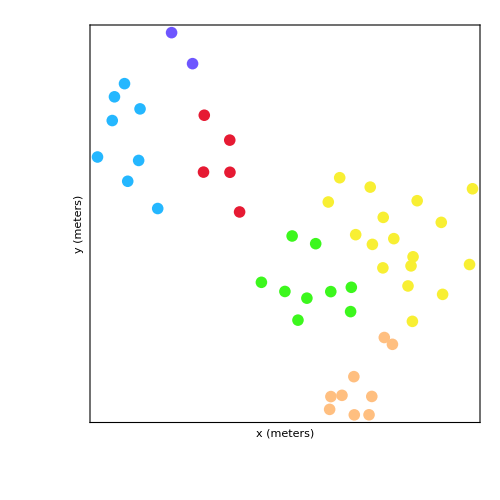

```mathematica
(*This is a very basic algorithm to generate points in a landscape. Replace it with a better later on.*)
{sampledCoordinates,names,pops,cities}=GenerateAccumulatedCoordinates[-100,citiesNumber];
distances = CalculateEuclideanDistances[sampledCoordinates];
(*Geo-Clustering*)
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
clustersStrings=Table[ToString/@Flatten[Position[cities[[All,2]],#]&/@clusteredCoordinates[[i]]],{i,1,clusteredCoordinates//Length}]
clustersIDs=Position[Map[ToExpression,clustersStrings,Infinity],#][[1,1]]&/@Range[Length[sampledCoordinates]];
(*Plots*)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clustersStrings])]]//Flatten//RandomSample;
ListPlot[clusteredCoordinates,PlotTheme->"RandomPointsPlot",ImageSize->500,PlotStyle->colors]
```

## Analyze

Map

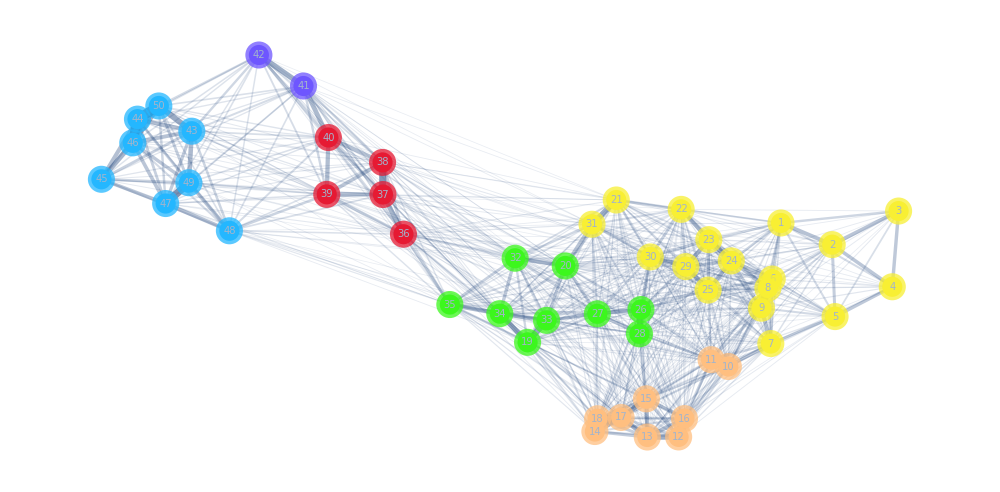

```mathematica
(*This "migration" is replacing the real kernel for the time being. It is based on the inverse of the distance to other nodes.*)
migration = CalculateMigrationProbabilities[distances, .05];
edgeshape2[e_,___]:={Arrowheads[{{.000001,.9}}],Arrow[e]}
stylesSwatch=Directive[Opacity[1],colors[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[clusteredCoordinates//Length];
stylesList=(ToString[#[[1]]]->stylesSwatch[[#[[2]]]])&/@Transpose[{Range[clustersIDs//Length],clustersIDs}];
map = GraphTransitionsFrequenciesWithMax[
  {
Chop[ReplacePart[migration,{i_,i_}->0]//LowerTriangularize,10^-2],
ToString /@ Range[Length[migration]]
   }, .15,
 VertexStyle ->stylesList,
VertexCoordinates ->sampledCoordinates,
VertexSize ->1vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize -> 1000,
LineThickness -> .0075,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

```mathematica
Export["00_clustering.pdf",map,ImageSize->2000,ImageResolution->500]
```

00_clustering.pdf

Mask Movement with Site-Types

```mathematica
(*If the transition between city types is not possible, or improbable, then mask it with the corresponding value. After that, normalize for the probabilities to still add up to one.*)
cityType=RandomChoice[Range[classesNumber],sampledCoordinates//Length]
{cityType[[1]],#}&/@cityType;
```

{1,2,4,1,4,3,3,2,2,3,1,2,2,3,4,1,1,3,1,1,2,2,2,3,1,3,2,2,3,3,4,1,2,3,3,2,3,3,2,3,1,4,1,4,1,4,4,1,2,2}

```mathematica
penalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}];
normalizedMaskedMatrix=(#/Total[#])&/@(penalizationsMask*migration);
(*Plots*)
penalizationsMaskPlot=penalizationsMask//MatrixPlot[#,ColorFunction -> "LakeColors", ImageSize ->500/2]&;
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/classesNumber]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
normalizedMaskedMatrixPlot=normalizedMaskedMatrix//MatrixPlot[#,ColorFunction->"LakeColors"]&;
```

Movement Network

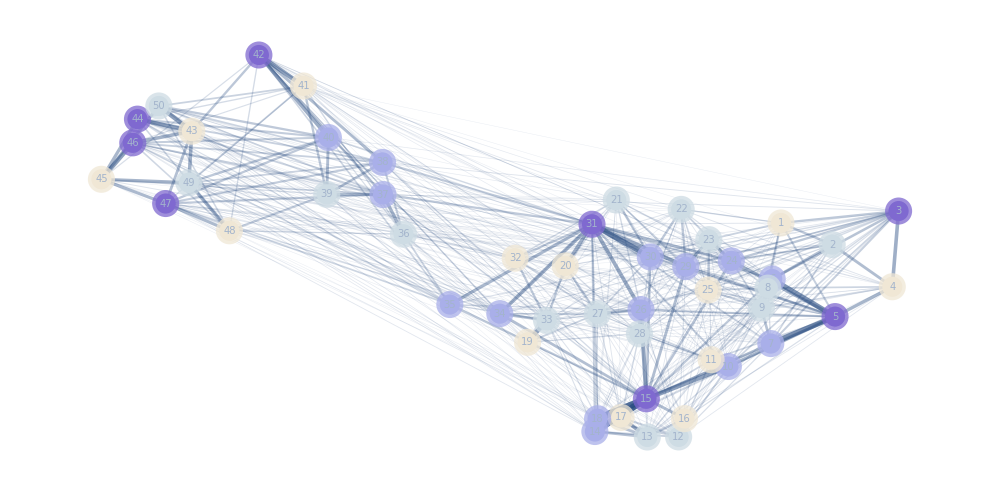

01_Movement.pdf

```mathematica
edgeshape2[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .5,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize ->vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize->1000,
LineThickness->.005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
Export["01_Movement.pdf",%,ImageSize->2000,ImageResolution->500]
```

Sink and Source

```mathematica
differenceThreshold=.3;
(**)
communities=Map[ToExpression,clustersStrings,Infinity]
outCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[normalizedMaskedMatrix,{i_,i_}->0];
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
inCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[normalizedMaskedMatrix,{i_,i_}->0]//Transpose;
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
outMinusIn=outCommunity-inCommunity;
typeOfCommunity=If[Abs[#]<differenceThreshold,"Bridge",If[#>0,"Source","Sink"]]&/@outMinusIn
(**)
gridSourceSink=Grid[{
Style[PaddedForm[#,{3,3}],7.5,Bold]&/@outMinusIn,
Style[#,7.5,Bold]&/@typeOfCommunity
},
Frame->True,Background->{Lighter[#,0.1]&/@colors[[1;;Length[outMinusIn]]],None},ItemSize->3]
edges=Table[colors[[i]]&/@clustersStrings[[i]],{i,1,Length[clustersStrings]}]//Flatten;
flattenedRatios=Table[ConstantArray[typeOfCommunity[[i]],communities[[i]]//Length],{i,1,communities//Length}]//Flatten;
graphSinkSource=HighlightGraph[graph, Style[#[[2]] ,Directive[EdgeForm[Directive[Opacity[1],Switch[#[[3]],"Bridge",Black,"Sink",Darker[Blue,0],"Source",Darker[Red,0]],Thickness[.005]]],#[[1]]]] & /@ ({edges,clustersStrings//Flatten,flattenedRatios} // Transpose)];
```

{{1,2,3,4,5,6,7,8,9,21,22,23,24,25,29,30,31},{10,11,12,13,14,15,16,17,18},{19,20,26,27,28,32,33,34,35},{36,37,38,39,40},{41,42},{43,44,45,46,47,48,49,50}}

{Sink,Sink,Source,Source,Bridge,Bridge}

-1.920 | -0.569 |  1.490 |  0.778 | -0.037 |  0.256
Sink | Sink | Source | Source | Bridge | Bridge

Sinks and Sources Report

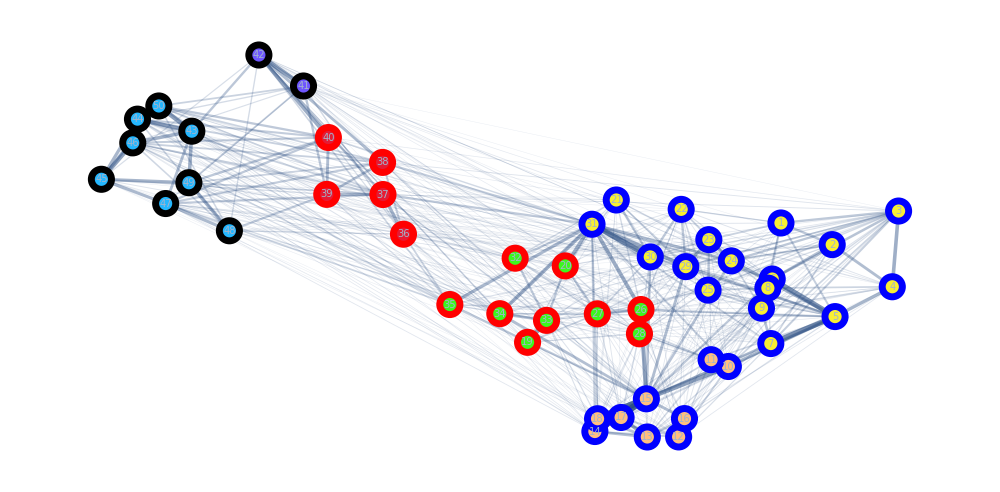
Clustered Map |  | Point Types |  | Sources (R) and Sinks(B)
-Graphics- | + | -Graphics- | = | -Graphics-
-1.920 | -0.569 |  1.490 |  0.778 | -0.037 |  0.256
Sink | Sink | Source | Source | Bridge | Bridge

02_grid.pdf

```mathematica
gridSinksAndSources=Grid[{
Style[#,25]&/@{"Clustered Map","","Point Types","","Sources (R) and Sinks(B)"},
{map,Style["+",Bold,50],graph,Style["=",Bold,50],Grid[{{graphSinkSource},{gridSourceSink}}]}
}]
Export["02_grid.pdf",%]
```

Centrality Analysis

```mathematica
BetweennessCentrality[map]
a=HighlightGraph[map,VertexList[map],VertexSize-> Thread[VertexList[map]-> Rescale[%]]];
BetweennessCentrality[graph]
b=HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]-> Rescale[%]]];
Grid[{{a,b}}]
```

{0.,0.,0.,0.233766,3.52049,8.90401,8.90401,10.0704,10.0704,10.0704,6.09495,2.98556,1.70524,0.698385,2.23039,2.19985,0.783678,1.8743,11.986,13.9974,18.1595,16.6344,7.24801,7.24801,7.24801,9.51926,17.6314,6.43783,10.3727,13.3643,27.4915,36.2847,17.7215,32.4521,56.4294,73.6228,29.6787,26.3006,15.2618,12.7811,10.6548,9.0949,0.510226,0.,0.318176,0.,0.514742,2.17581,0.514742,0.}

{46.5228,42.9182,175.603,46.5228,153.858,76.799,76.799,34.2297,44.5135,76.799,58.0629,65.2629,65.2629,72.1915,153.858,36.0109,58.0629,79.4551,113.638,124.812,93.8934,65.2629,52.3887,82.1012,58.0629,87.8488,88.8941,65.2629,87.8488,87.8488,196.654,145.301,117.146,72.6169,65.3533,52.5376,34.9757,34.9757,48.6841,29.3873,127.241,182.685,39.7309,132.114,71.7098,132.114,132.114,88.3226,44.613,35.1305}

-Graphics-

```mathematica
ClosenessCentrality[map]
a=HighlightGraph[map,VertexList[map],VertexSize-> Thread[VertexList[map]-> Rescale[%]]];
ClosenessCentrality[graph]
b=HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]-> Rescale[%]]];
Grid[{{a,b}}]
```

{0.,17.7563,22.4402,23.2074,27.3531,40.1686,38.8909,31.6658,23.1922,42.9599,29.7836,51.6569,37.1436,43.5519,36.6264,34.6062,30.3041,33.2226,53.2707,59.218,62.6115,59.6773,56.2839,51.5371,48.505,48.9232,47.7349,40.4287,45.8533,41.329,51.4625,57.0557,50.1121,51.7919,51.0336,52.9256,47.324,43.2968,40.3526,40.0332,41.8451,42.0804,36.8297,36.4446,37.9135,32.4786,39.0364,40.7086,35.2243,33.0001}

{7.85364,6.69289,8.49126,7.60247,7.24498,7.6423,7.76803,6.2413,6.68568,7.4389,7.17162,6.39101,6.71715,7.37117,7.77466,7.70625,7.75769,7.58973,8.07596,7.70521,7.97771,6.81177,6.79972,7.05465,7.44701,7.01036,7.6238,6.88187,6.91816,7.17314,8.90864,8.09523,8.3763,6.07916,5.9992,7.22971,6.37605,6.41878,6.95211,7.03689,8.87355,8.63691,7.21066,7.53569,8.54525,7.77967,7.48074,8.55611,7.62838,7.68612}

-Graphics-

Walkers

```mathematica
kernel=normalizedMaskedMatrix;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,3->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
```

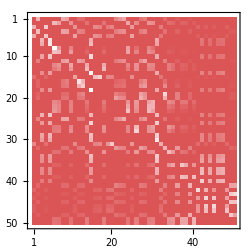
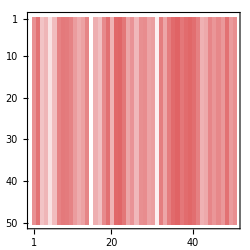
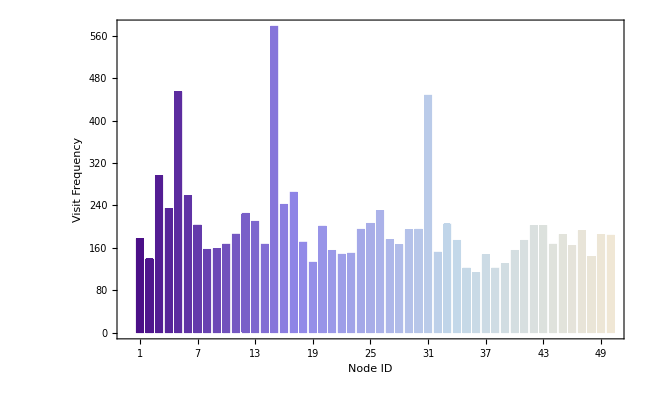
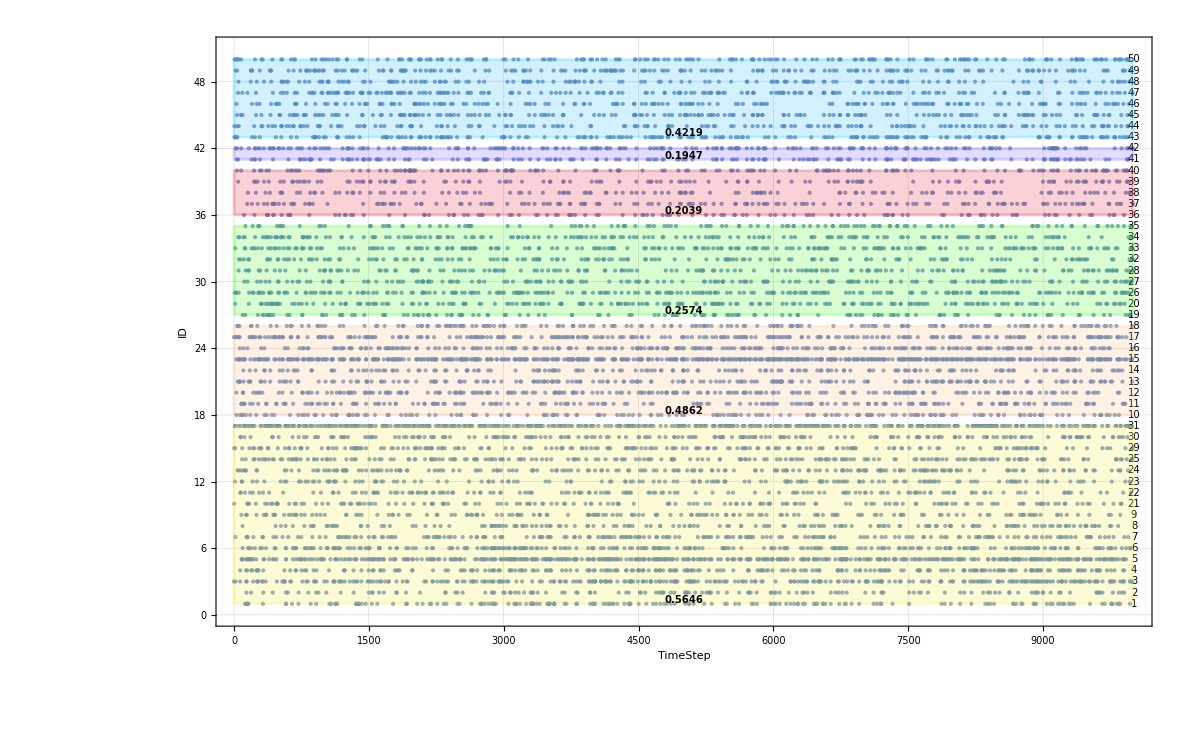
Transitions | Limiting
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(**)
data=RandomFunction[markov,{0,10000}];
tally=(data//Normal)[[All,All,2]][[1]]//Tally//Sort;
barChartFrequency=BarChart[tally[[All,2]],
ChartStyle->"LakeColors",
ChartLabels->tally[[All,1]],
ImageSize->650,
Frame->True,
FrameStyle->Thick,
FrameTicksStyle->Directive[8],
FrameLabel->(Style[#,25]&/@{"Node ID","Visit Frequency"})
];
songs=ListPlotSongWithCommunities[(data//Normal)[[1,All,2]],Map[ToExpression,clustersStrings,Infinity],colors,ImageSize->1200,TextSize->10];
{Range[Length[kernel]],MarkovProcessProperties[markov,"HoldingTimeMean"]}//MatrixForm;
limitMatrix=MarkovProcessProperties[markov,"LimitTransitionMatrix"]//MatrixPlot[#,PlotLegends->Placed[Automatic,Below],ColorFunction->"CherryTones",ImageSize->250]&;
transitionsMatrix=MarkovProcessProperties[markov,"TransitionMatrix"]//MatrixPlot[#,PlotLegends->Placed[Automatic,Below],ColorFunction->"CherryTones",ImageSize->250]&;
matricesGrid=Grid[{Style[#,15]&/@{"Transitions","Limiting"},{transitionsMatrix,limitMatrix}}];
gridRandomWalker=Grid[{{Grid[{{matricesGrid},{barChartFrequency}}],songs}}]
```

Markov

```mathematica
MarkovProcessProperties[markov,"LimitTransitionMatrix"][[1]];
```

```mathematica
trans=Transpose[kernel];
{eVals,eVecs}=Eigensystem[trans]//N;
Normalize[eVecs[[1]],Total];
```

Normalize::nlnfa: The second argument Total is not a norm function that always returns a non-negative real number for any numeric argument.

{0.00488118,0.00658256,0.00697057,0.00658549,0.00695844,0.00702538,0.00694683,0.00683611,0.00713778,0.00623566,0.00612721,0.00555029,0.00656514,0.00647771,0.0075888,0.00772505,0.00881134,0.0081802,0.00843951,0.00804123,0.00680641,0.00796503,0.00607277,0.00503781,0.00600072,0.0072729,0.0077681,0.00778968,0.00913751,0.00962492,0.00954782,0.010258,0.0073532,0.00742183,0.00768084,0.00702183,0.00686208,0.00808992,0.00969983,0.00860924,0.00841474,0.00868928,0.00868928,0.00800116,0.0074458,0.00729027,0.00733787,0.00673993,0.00693419,0.00805287,0.00883082,0.00966258,0.00988196,0.00973753,0.00827316,0.0105584,0.00793277,0.00774026,0.00821691,0.00651339,0.00636418,0.00708396,0.00778645,0.00864733,0.00965962,0.00947658,0.0103923,0.00848175,0.00823459,0.00907857,0.00769917,0.00699823,0.00662016,0.00758015,0.00838576,0.00861798,0.00847322,0.00883778,0.0104214,0.0106314,0.00795945,0.00805647,0.00734658,0.00688452,0.00590665,0.00731739,0.00793054,0.00752525,0.00840334,0.00843692,0.00843692,0.0087068,0.0075663,0.00818745,0.0068742,0.00565835,0.00549672,0.00613735,0.00649083,0.00725478,0.00834874,0.00833527,0.00793056,0.00765036,0.0100861,0.00683479,0.00677953,0.00516361,0.00496408,0.00731685,0.0064229,0.00708756,0.00704601,0.0075922,0.00616364,0.00686602,0.00682179,0.00818715,0.00749863,0.00620158,0.00581292,0.00556582,0.0082754,0.00566962,0.00572149,0.00581929,0.00873008,0.00795521,0.00766306,0.00845861,0.00467002,0.00568371}

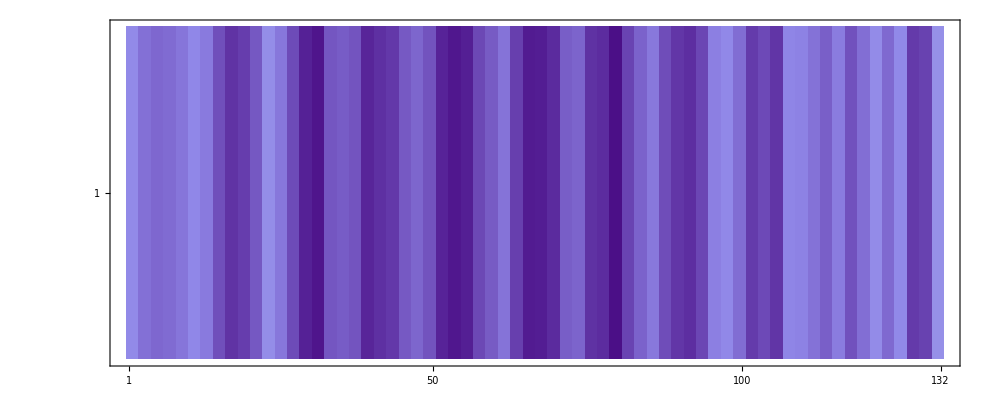

```mathematica
markov=DiscreteMarkovProcess[initialState,kernel];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length]
MatrixPlot[{markovPDF},ColorFunction->ColorData[{"LakeColors","Reverse"}],ImageSize->1000]
(*MatrixPlot[{tally[[All,2]]},ColorFunction->ColorData[{"LakeColors","Reverse"}],ImageSize->1000]*)
```

```mathematica
{Range[markov[[1]]//Length],markovPDF}//Transpose
```

{{1,0.00488118},{2,0.00658256},{3,0.00697057},{4,0.00658549},{5,0.00695844},{6,0.00702538},{7,0.00694683},{8,0.00683611},{9,0.00713778},{10,0.00623566},{11,0.00612721},{12,0.00555029},{13,0.00656514},{14,0.00647771},{15,0.0075888},{16,0.00772505},{17,0.00881134},{18,0.0081802},{19,0.00843951},{20,0.00804123},{21,0.00680641},{22,0.00796503},{23,0.00607277},{24,0.00503781},{25,0.00600072},{26,0.0072729},{27,0.0077681},{28,0.00778968},{29,0.00913751},{30,0.00962492},{31,0.00954782},{32,0.010258},{33,0.0073532},{34,0.00742183},{35,0.00768084},{36,0.00702183},{37,0.00686208},{38,0.00808992},{39,0.00969983},{40,0.00860924},{41,0.00841474},{42,0.00868928},{43,0.00868928},{44,0.00800116},{45,0.0074458},{46,0.00729027},{47,0.00733787},{48,0.00673993},{49,0.00693419},{50,0.00805287},{51,0.00883082},{52,0.00966258},{53,0.00988196},{54,0.00973753},{55,0.00827316},{56,0.0105584},{57,0.00793277},{58,0.00774026},{59,0.00821691},{60,0.00651339},{61,0.00636418},{62,0.00708396},{63,0.00778645},{64,0.00864733},{65,0.00965962},{66,0.00947658},{67,0.0103923},{68,0.00848175},{69,0.00823459},{70,0.00907857},{71,0.00769917},{72,0.00699823},{73,0.00662016},{74,0.00758015},{75,0.00838576},{76,0.00861798},{77,0.00847322},{78,0.00883778},{79,0.0104214},{80,0.0106314},{81,0.00795945},{82,0.00805647},{83,0.00734658},{84,0.00688452},{85,0.00590665},{86,0.00731739},{87,0.00793054},{88,0.00752525},{89,0.00840334},{90,0.00843692},{91,0.00843692},{92,0.0087068},{93,0.0075663},{94,0.00818745},{95,0.0068742},{96,0.00565835},{97,0.00549672},{98,0.00613735},{99,0.00649083},{100,0.00725478},{101,0.00834874},{102,0.00833527},{103,0.00793056},{104,0.00765036},{105,0.0100861},{106,0.00683479},{107,0.00677953},{108,0.00516361},{109,0.00496408},{110,0.00731685},{111,0.0064229},{112,0.00708756},{113,0.00704601},{114,0.0075922},{115,0.00616364},{116,0.00686602},{117,0.00682179},{118,0.00818715},{119,0.00749863},{120,0.00620158},{121,0.00581292},{122,0.00556582},{123,0.0082754},{124,0.00566962},{125,0.00572149},{126,0.00581929},{127,0.00873008},{128,0.00795521},{129,0.00766306},{130,0.00845861},{131,0.00467002},{132,0.00568371}}

```mathematica
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.0025]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
edgeshape2[e_,___]:={Arrowheads[{{.0075,.8}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .25,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize -> Thread[VertexList[graph]->10*Log[1.5+3*Rescale[markovPDF]]],
VertexLabelStyle->6.5,
ImageSize->1000,
LineThickness->.0005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
Export["03_MarkovStationary.pdf",%]
```

-Graphics-

03_MarkovStationary.pdf

## Export Report

```mathematica
Grid[{{gridSinksAndSources},{gridRandomWalker}}]
Export["NetworkReport"<>StringPadLeft[ToString[(directionStrength*100)//Round],3,"0"]<>".pdf",%,ImageSize->5000,ImageResolution->500]
```